```mathematica
ClearAll["Global`*"]

(* Script outputs a rational polynomial fit of thermodynamic variables given by lattice qcd eos *)
(* Run cform.sh and then copy-paste fits to equation_of_state class functions in rhic/src/EquationOfState.cpp *)

(* Functions in equation_of_state class (no argument means it's a function of energy density)*)

(* Lattice QCD functions *)
(* equilbrium_pressure *)
(* speed_of_sound_squared() *)
(* effective_temperature()  *)

(* Quasiparticle functions *)
(* z_quasi() *)
(* mdmde_quasi() *)
(* equilibrium_mean_field() *)

(* Shear-bulk relaxation time coefficients. Where/how did I compute these? *)
(* beta_shear(T) *)
(* beta_bulk(T) *)

(* This is in rhic/src/EquationOfState.cpp but not part of equation_of_state class *)
(* equilibrium_energy_density(T) *)

Nf=3;
eg=16.Pi^2/30.;
eq=6.*3*7Pi^2/120.;  (*check these later*)
sFac = eg+eq 

(* plot styles *)
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[3.5]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

(* rational polynomial fit module *)
rationalPolyFit[data_,NN_,MM_]:=Module[{a,b,varsa,varsb,vars,sol,varsc,varsd,Q},
varsa=Table[a[n],{n,0,NN}];
varsb=Table[b[m],{m,0,MM}];
vars=Join[varsa,varsb];
sol=FindFit[data,Sum[a[n]x^n,{n,0,NN}]/Sum[b[m]x^m,{m,0,MM}],vars,x,MaxIterations->10000];
varsc=varsa/.sol;
varsd=varsb/.sol;
Return[Sum[varsc[[n+1]]x^n,{n,0,NN}]/Sum[varsd[[m+1]]x^m,{m,0,MM}]];
];


wd=SetDirectory@NotebookDirectory[];
eosData=Import[wd<>"/eos_hotqcd_smash.dat"];
```

15.6269

563.822

168.334

T min = 0.247529 fm^-1 or 0.0488442 GeV

T max = 5.07585 fm^-1 or 1.0016 GeV

energy min = 0.00174018 fm^-4

energy max = 9700.53 fm^-4

pressure min = 0.000358146 fm^-4

pressure max = 3119.57 fm^-4

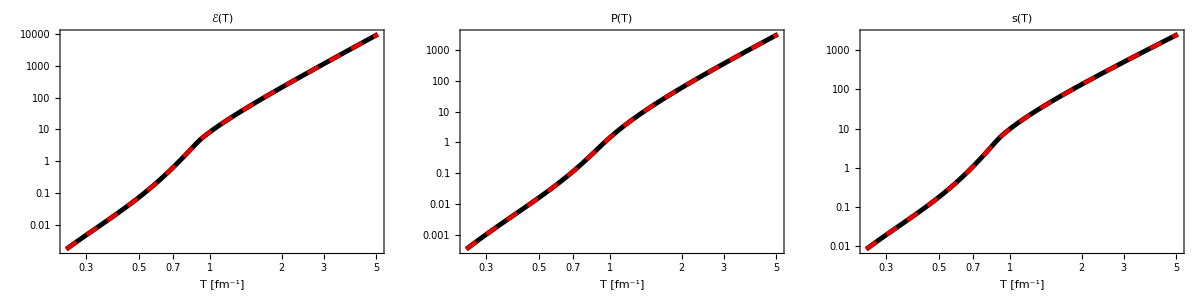

```mathematica
(* Hot QCD + Smash EoS data columns *)
(* T = [0.050 GeV, 1.0 GeV] *)

(* 1 = e  [GeV.fm^-3] *)
(* 2 = p  [GeV.fm^-3] *)
(* 3 = s  [fm^-3] *)
(* 4 = T  [GeV]  *)

(* convert all GeV units to fm^-1 *)
GeVtoInversefm =  1./0.197326938;  
energy= GeVtoInversefm *eosData[[All,1]];
pressure=GeVtoInversefm *eosData[[All,2]];
entropy=eosData[[All,3]];
temp =GeVtoInversefm * eosData[[All,4]];
Export["beta_coefficients/temperature.dat",Join[{Length[temp]},temp]];

Tmin=temp[[1]];
Tmax=temp[[-1]];
etemp1=Interpolation[Table[{temp[[i]],energy[[i]]},{i,1,Length[temp]}]];
Ptemp1=Interpolation[Table[{temp[[i]],pressure[[i]]},{i,1,Length[temp]}]];
Sfit1=Interpolation[Table[{temp[[i]],entropy[[i]]},{i,1,Length[temp]}]];
(* check whether entropy density makes sense to old eos *)
etemp=etemp1;
Ptemp=Ptemp1;

(* the data file is too big. do uniform ΔT = 0.5 MeV intervals *)
(*temp=Table[GeVtoInversefm(0.05+0.0005*i),{i,0,1900}];*)
(*temp=Table[GeVtoInversefm(0.05+0.001*i),{i,0,950}];
energy=Table[etemp1[temp[[i]]],{i,1,Length[temp]}];
pressure=Table[Ptemp1[temp[[i]]],{i,1,Length[temp]}];

etemp=Interpolation[Table[{temp[[i]],energy[[i]]},{i,1,Length[temp]}]];
Ptemp=Interpolation[Table[{temp[[i]],pressure[[i]]},{i,1,Length[temp]}]];*)
(*Sfit=Interpolation[Table[{temp[[i]],Sfit1[temp[[i]]]},{i,1,Length[temp]}]];*)
(*Sfit[T_]:=(etemp[T]+Ptemp[T])/T;*)

emin=etemp[Tmin];
emax=etemp[Tmax];
etemp[0.5*GeVtoInversefm]
Ptemp[0.5*GeVtoInversefm]
Print["T min = ",Tmin," fm^-1 or ",Tmin/GeVtoInversefm," GeV"]
Print["T max = ",Tmax," fm^-1 or ",Tmax/GeVtoInversefm," GeV"]
Print[]
Print["energy min = ",etemp[Tmin]," fm^-4"]
Print["energy max = ",etemp[Tmax]," fm^-4"]
Print[""]
Print["pressure min = ",Ptemp[Tmin]," fm^-4"]
Print["pressure max = ",Ptemp[Tmax]," fm^-4"]

(* Check that the modified functions are the same *)
Grid[{{LogLogPlot[{etemp[T],etemp1[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLogPlot[{Ptemp[T],Ptemp1[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLogPlot[{Sfit1[T],(etemp[T]+Ptemp[T])/T},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["s(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
```

0.00174018	0.00168795

567.583		567.583

9700.53		9700.53

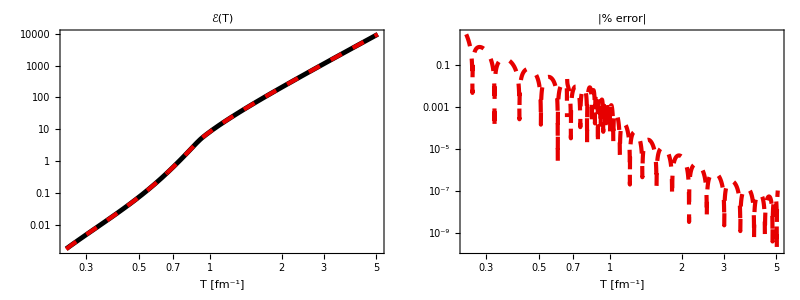

```mathematica
(*** e(T) fit ***)
edata=Table[{temp[[i]],energy[[i]]},{i,1,Length[temp]}];
n =18;
efit[T_]=rationalPolyFit[edata,n,n]/.{x->T};

Print[etemp[Tmin],"\t",efit[Tmin]]
Print[etemp[Tmax/2],"\t\t",efit[Tmax/2]]
Print[etemp[Tmax],"\t\t",efit[Tmax]]

Grid[{{
LogLogPlot[{etemp[T],efit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["ℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLogPlot[{100*Abs[(etemp[T]-efit[T])/etemp[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
Export["energy.txt",CForm[efit[T]]];
```

0.000358146	0.000360232

169.51		169.51

3119.57		3119.57

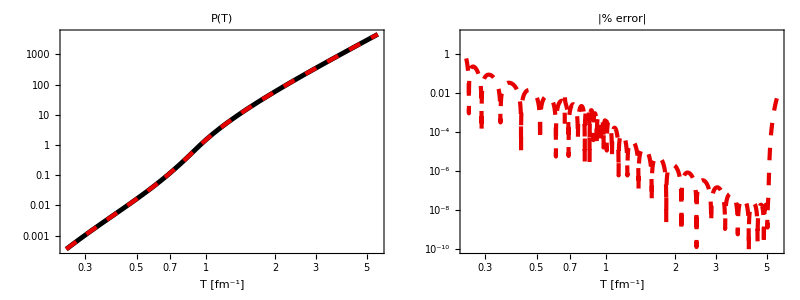

```mathematica
(*** P(T) fit ***)
pdata=Table[{temp[[i]],pressure[[i]]},{i,1,Length[temp]}];
n =18;
Pfit[T_]=rationalPolyFit[pdata,n,n]/.{x->T};

Print[Ptemp[Tmin],"\t",Pfit[Tmin]]
Print[Ptemp[Tmax/2],"\t\t",Pfit[Tmax/2]]
Print[Ptemp[Tmax],"\t\t",Pfit[Tmax]]

Grid[{{
LogLogPlot[{Ptemp[T],Pfit[T]},{T,Tmin,1.1Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["P(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLogPlot[{100*Abs[(Ptemp[T]-Pfit[T])/Ptemp[T]]},{T,Tmin,1.1Tmax},PlotRange->{10^-10,10},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
Export["pressure.txt",CForm[Pfit[T]]];
```

0.223461	0.223451

0.312689		0.31269

0.325737		0.325736

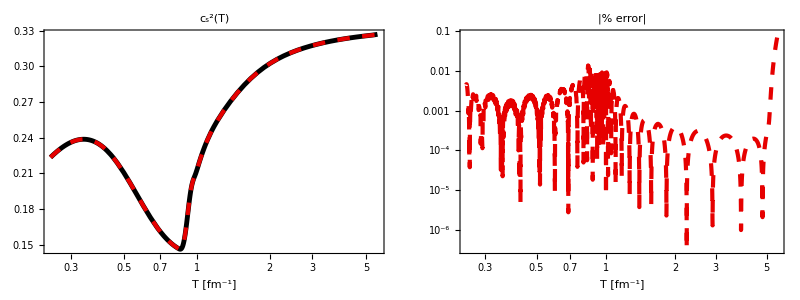

```mathematica
(*** Subscript[c, s]^2(T) fit ***)
(* Subscript[c, s]^2 = dp/de = dp/dT dT/de = s dT/de= s/(de/dT) *)

cs2temp[T_]=Sfit1[T]/etemp'[T];
cs2data=Table[{temp[[i]],cs2temp[temp[[i]]]},{i,1,Length[temp]}];
n =18;
cs2fit[T_]=rationalPolyFit[cs2data,n,n]/.{x->T};

Print[cs2temp[Tmin],"\t",cs2fit[Tmin]]
Print[cs2temp[Tmax/2],"\t\t",cs2fit[Tmax/2]]
Print[cs2temp[Tmax],"\t\t",cs2fit[Tmax]]

Grid[{{
LogLinearPlot[{cs2temp[T],cs2fit[T]},{T,Tmin,1.1Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["c_s^2(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLogPlot[{100*Abs[(cs2temp[T]-cs2fit[T])/cs2temp[T]]},{T,Tmin,1.1Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]
Export["cs2.txt",CForm[cs2fit[T]]];
```

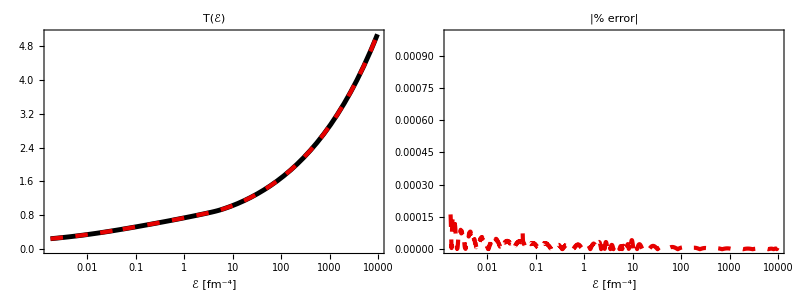

```mathematica
(*** T(e) fit ***)

Tdata=Table[{etemp[temp[[i]]],temp[[i]]},{i,1,Length[temp]}];
Tfunc=Interpolation[Tdata];

n =24;
Tfit[e_]=rationalPolyFit[Tdata,n,n]/.{x->e};

Grid[{{
LogLinearPlot[{Tfunc[e],Tfit[e]},{e,emin,emax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["T(ℰ)",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
LogLinearPlot[{100*Abs[(Tfunc[e]-Tfit[e])/Tfunc[e]]},{e,emin,emax},PlotRange->{0,0.001},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"ℰ [fm^-4]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["temperature.txt",CForm[Tfit[e]]];
```

0.791709

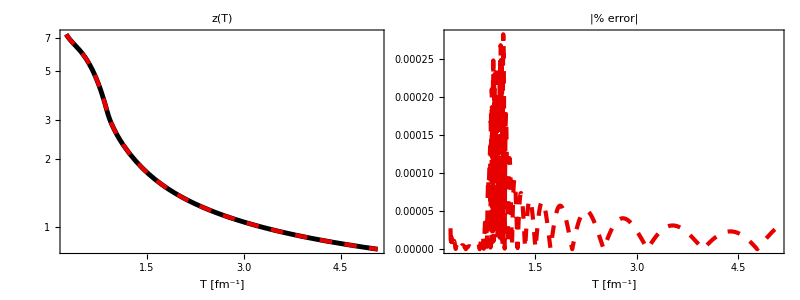

```mathematica
(*** z(e) fit ***)

Nc = 3.0;
g =Pi^4/180.0*(4.*(Nc^2-1.)+7.0*Nc*Nf);
F[T_]=(2.*Pi^2)/g*Sfit1[T]/T^3;

zStart=0.79;
zQuasi=Table[{temp[[i]],""},{i,1,Length[temp]}];
zQuasi[[Length[zQuasi],2]]=x/.FindRoot[x^3*BesselK[3,x]==F[temp[[-1]]],{x,zStart},MaxIterations->5000];
zQuasi[[-1,2]]
For[i = Length[zQuasi]-1, i >0,i--,
zQuasi[[i,2]]=x/.FindRoot[x^3*BesselK[3,x]==F[zQuasi[[i,1]]],{x,zQuasi[[i+1,2]]},MaxIterations->5000];
]
zQuasifunc=Interpolation[zQuasi];

n =20;
zQuasifit[T_]=rationalPolyFit[zQuasi,n,n]/.{x->T};

Grid[{{
LogPlot[{zQuasifunc[T],zQuasifit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["z(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{100*Abs[(zQuasifunc[T]-zQuasifit[T])/zQuasifunc[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|% error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["zquasi.txt",CForm[zQuasifit[T]]];
```

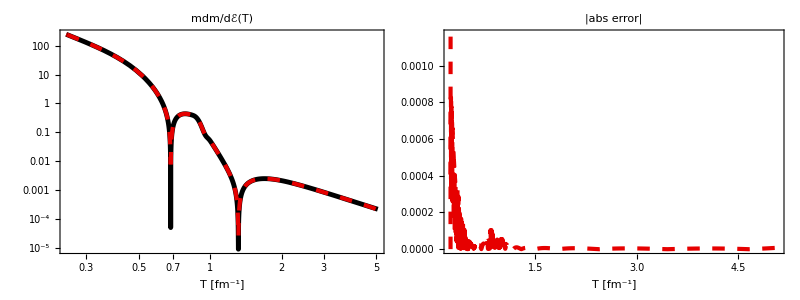

```mathematica
(*** m dm/de(T) fit ***) 

mQuasifunc[T_] =T*zQuasifunc[T]; 
mdmde[T_]=(mQuasifunc[T]*mQuasifunc'[T])/etemp'[T];
mdmdedata=Table[{temp[[i]],mdmde[temp[[i]]]},{i,1,Length[temp]}];

n =22;
mdmdefit[T_]=rationalPolyFit[mdmdedata,n,n]/.{x->T};

Grid[{{LogLogPlot[{Abs[mdmde[T]],Abs[mdmdefit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["mdm/dℰ(T)",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75],
Plot[{Abs[(mdmde[T]-mdmdefit[T])]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->320,Frame->True,PlotLabel->Style["|abs error|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->14},AspectRatio->0.75]}}]

Export["mdmde.txt",CForm[mdmdefit[T]]];
```

-4.79403

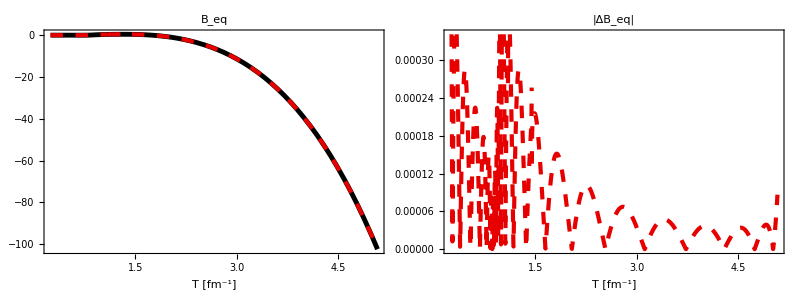

```mathematica
(*** Subscript[B, eq](T) fit ***)

Pquasi[T_]=(g*T^4)/(2.*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]]; (* equilibrium kinetic pressure *)
Beq=Table[{temp[[i]],Pquasi[temp[[i]]]-Ptemp[temp[[i]]]},{i,1,Length[temp]}];
Beqfunc=Interpolation[Beq];

n=22;
Beqfit[T_]=rationalPolyFit[Beq,n,n]/.{x->T};

Beqfunc[0.5*GeVtoInversefm]

Grid[{{
Plot[{Beqfunc[T],Beqfit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["B_eq",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{Abs[Beqfunc[T]-Beqfit[T]]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|ΔB_eq|",FontSize->20],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["Beq.txt",CForm[Beqfit[T]]];
```

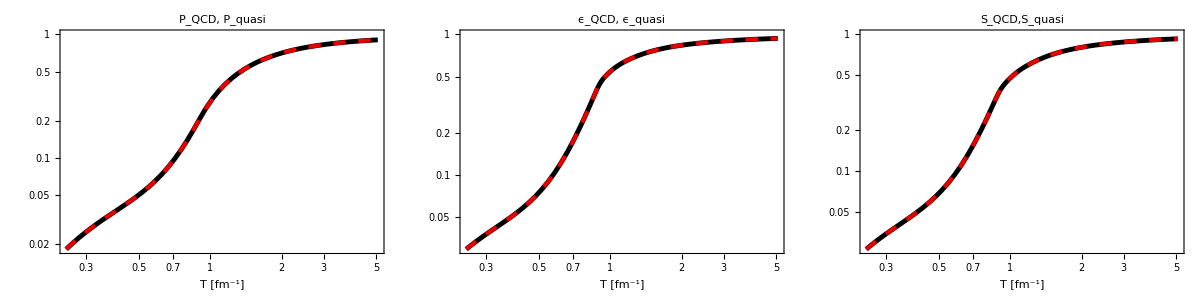

```mathematica
(* check thermodynamic consistency *)
Pquasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*BesselK[2,zQuasifunc[T]] -Beqfunc[T];
Equasi[T_]=(g*T^4)/(2.0*Pi^2)*zQuasifunc[T]^2*(3.0*BesselK[2,zQuasifunc[T]]+zQuasifunc[T]*BesselK[1,zQuasifunc[T]])+Beqfunc[T];
SQuasi[T_]=(Pquasi[T]+Equasi[T])/T;

Grid[{{LogLogPlot[{Ptemp[T]/(sFac T^4/3),Pquasi[T]/(sFac T^4/3)(*,Beqfunc[T]/(sFac T^4/3),(Pquasi[T]+Beqfunc[T])/(sFac T^4/3)*)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"P_QCD, P_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{etemp[T]/(sFac T^4),Equasi[T]/(sFac T^4)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"ϵ_QCD, ϵ_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75],
LogLogPlot[{Sfit1[T]/(4*sFac*T^3/3),SQuasi[T]/(4*sFac*T^3/3)},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,FrameLabel->{"T [fm^-1]",""},PlotLabel->"S_QCD,S_quasi",BaseStyle->{FontSize->16},AspectRatio->0.75]}}]
```

134.589

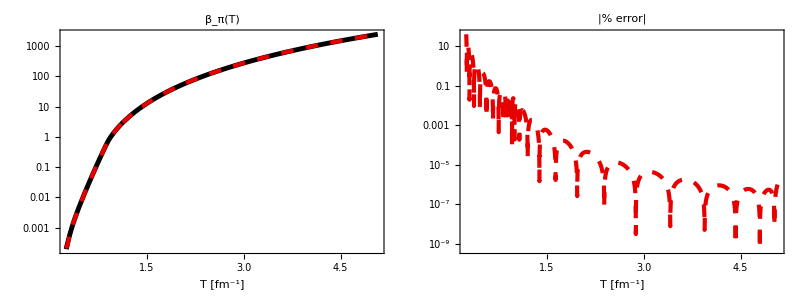

```mathematica
wd=SetDirectory@NotebookDirectory[];
betapiData=Import[wd<>"/beta_coefficients/results/betapi.dat"];
betapi = Interpolation[betapiData];
GeVtoInversefm =  1./0.197326938;  
n = 22;
(*n = 22 *)
betapifit[T_]=rationalPolyFit[betapiData,n,n]/.{x->T};
betapi[0.5*GeVtoInversefm]
Grid[{{LogPlot[{betapi[T],betapifit[T]},{T,Tmin,Tmax},PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["β_π(T)",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
LogPlot[{100*Abs[(betapi[T]-betapifit[T])/betapi[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,Axes->False,PlotLabel->Style["|% error|",FontSize->24],FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["betapi.txt",CForm[betapifit[T]]];
```

1.81005

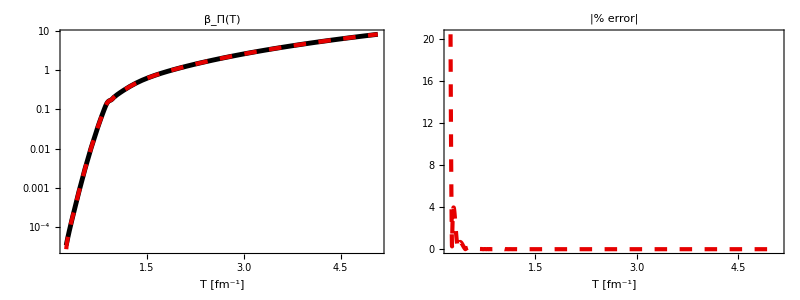

```mathematica
wd=SetDirectory@NotebookDirectory[];
I11 = Interpolation[Import[wd<>"/beta_coefficients/results/I11.dat"]];
betabulk[T_]=5./3.*betapi[T]+cs2temp[T]*(mQuasifunc[T]*mQuasifunc'[T]*I11[T] - (etemp[T]+Ptemp[T]));
betabulkData=Table[{temp[[i]],betabulk[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
betabulkfit[T_]=rationalPolyFit[betabulkData,n,n]/.{x->T};
betabulk[0.5*GeVtoInversefm]
Grid[{{
LogPlot[{betabulk[T],betabulkfit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["β_Π(T)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(betabulk[T]-betabulkfit[T])/betabulk[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["betabulk.txt",CForm[betabulkfit[T]]];
```

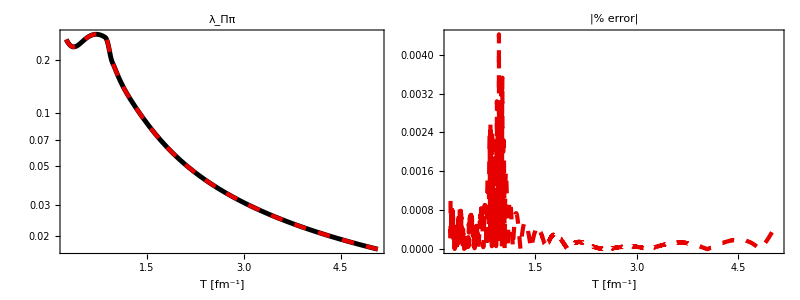

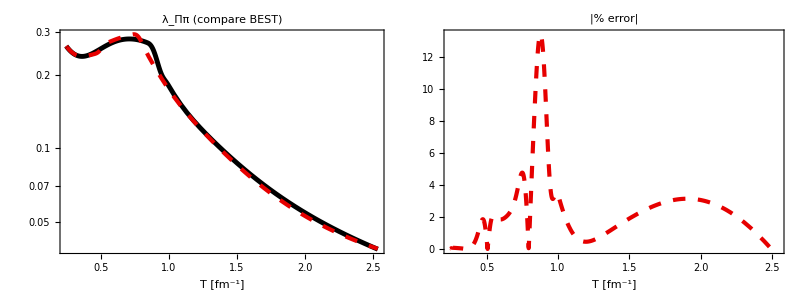

```mathematica
wd=SetDirectory@NotebookDirectory[];
cpibar= Interpolation[Import[wd<>"/beta_coefficients/results/cpi_bar.dat"]];
I22= Interpolation[Import[wd<>"/beta_coefficients/results/I22.dat"]];

lambdabulkpi[T_]=1./3. - cs2temp[T]  +  (mQuasifunc[T]^2*cpibar[T]*I22[T])/3.;

lambdabulkpiData=Table[{temp[[i]],lambdabulkpi[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
lambdabulkpifit[T_]=rationalPolyFit[lambdabulkpiData,n,n]/.{x->T};


lambdabulkpiBEST[T_]:=(-0.05108552557140905+1.1920234914279368*T-15.219316725127543*T^2+130.61531842041347*T^3-770.8911863265103*T^4+3118.871760309068*T^5-8468.953148265928*T^6+14145.287679451932*T^7-8803.791407406065*T^8-18733.99128349794*T^9+51682.35436183604*T^10-36637.21011161534*T^11-61257.49912224253*T^12+191225.24718245308*T^13-251340.30055725976*T^14+202939.1188463238*T^15-105685.13512860639*T^16+33524.63767044643*T^17-4874.2587031234525*T^18-365.5711567970833*T^19+185.5872650105065*T^20)/(-0.43047278991522+12.70413282512127*T-178.2263165530798*T^2+1509.5366934223478*T^3-8376.943970980205*T^4+31428.77486169897*T^5-79175.51654902888*T^6+124066.90852961707*T^7-80374.1971456783*T^8-103295.02037076751*T^9+265890.2087802455*T^10-98952.10428951876*T^11-390026.4365996752*T^12+644747.1964612629*T^13-182474.9416627948*T^14-671918.0845273717*T^15+1.1345950862087505*10^6*T^16-928481.0281592731*T^17+451241.4690115756*T^18-126100.26540849869*T^19+15861.53970099384*T^20);


Grid[{{
LogPlot[{lambdabulkpi[T],lambdabulkpifit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["λ_Ππ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(lambdabulkpi[T]-lambdabulkpifit[T])/lambdabulkpi[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Grid[{{
LogPlot[{lambdabulkpi[T],lambdabulkpiBEST[T]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["λ_Ππ (compare BEST)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(lambdabulkpi[T]-lambdabulkpiBEST[T])/lambdabulkpi[T]]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["lambdabulkpi.txt",CForm[lambdabulkpifit[T]]];
```

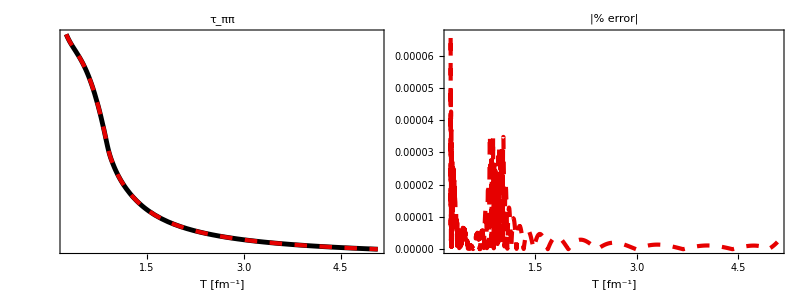

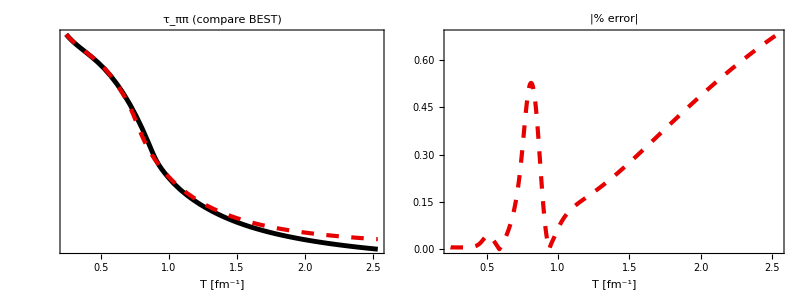

```mathematica
wd=SetDirectory@NotebookDirectory[];
cpibar= Interpolation[Import[wd<>"/beta_coefficients/results/cpi_bar.dat"]];
I22= Interpolation[Import[wd<>"/beta_coefficients/results/I22.dat"]];

taupipi[T_]=10./7.   +  (4.*mQuasifunc[T]^2*cpibar[T]*I22[T])/7.;

taupipiData=Table[{temp[[i]],taupipi[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
taupipifit[T_]=rationalPolyFit[taupipiData,n,n]/.{x->T};

taupipiBEST[T_]:=(89.41311519637208-1041.094113691887*T+4764.425117625884*T^2-10090.476443289059*T^3+8917.974251380117*T^4-13801.431906568394*T^5+83072.09022937233*T^6-183159.67600150174*T^7+28810.082526326736*T^8+498832.37222725525*T^9-699490.5306417008*T^10-254119.29595106983*T^11+1.7323548973462286*10^6*T^12-2.0899029775642569*10^6*T^13+1.0174068389595072*10^6*T^14+19083.15205472634*T^15+14222.166974284355*T^16-509848.2662136577*T^17+572523.795547174*T^18-266483.5357049334*T^19+47864.39550819899*T^20)/(47.27009609405139-491.15454407269385*T+1562.0632925957718*T^2+1608.4170703752723*T^3-24847.495447390378*T^4+72625.60281846905*T^5-89499.1223440185*T^6+1398.3882901031516*T^7+130534.35667663184*T^8-142739.4307650025*T^9+42048.92302717659*T^10+47516.79409529657*T^11-262474.21341655555*T^12+813625.9255959115*T^13-1.3757210900791723*10^6*T^14+1.2966474867523108*10^6*T^15-533652.0145401144*T^16-197061.1201749902*T^17+366672.47585666185*T^18-180554.15971412277*T^19+32754.915203308326*T^20);


Grid[{{
LogPlot[{taupipi[T],taupipifit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["τ_ππ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(taupipi[T]-taupipifit[T])/taupipi[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Grid[{{
LogPlot[{taupipi[T],taupipiBEST[T]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["τ_ππ (compare BEST)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(taupipi[T]-taupipiBEST[T])/taupipi[T]]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["taupipi.txt",CForm[taupipifit[T]]];
```

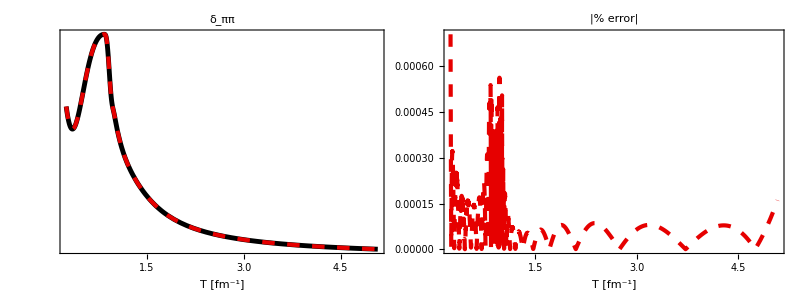

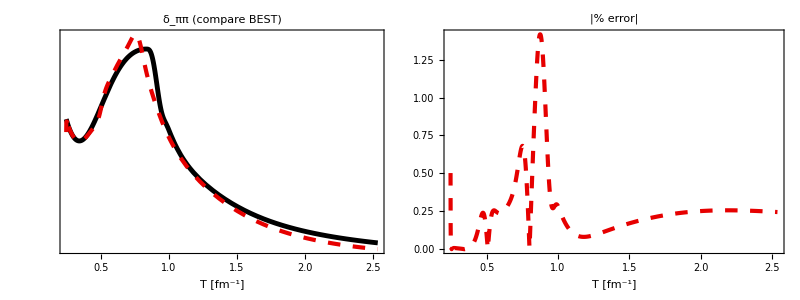

```mathematica
wd=SetDirectory@NotebookDirectory[];
cpibar= Interpolation[Import[wd<>"/beta_coefficients/results/cpi_bar.dat"]];
I22= Interpolation[Import[wd<>"/beta_coefficients/results/I22.dat"]];

deltapipi[T_]=4./3.  + cpibar[T]*I22[T](mQuasifunc[T]^2/3.-mdmde[T]*(etemp[T]+Ptemp[T])) ;

deltapipiData=Table[{temp[[i]],deltapipi[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
deltapipifit[T_]=rationalPolyFit[deltapipiData,n,n]/.{x->T};


deltapipiBEST[T_]:=(0.38988241949712893-8.39647991747567*T+78.64174583058013*T^2-417.04915480152675*T^3+1358.8678261634411*T^4-2769.3575306569605*T^5+3793.9294773679967*T^6-6494.90974085766*T^7+20619.860733197867*T^8-49821.02060139982*T^9+55754.66764111688*T^10+33820.7033277702*T^11-218000.59583932348*T^12+345691.6868052703*T^13-254644.01063959935*T^14-6596.2044403952605*T^15+213720.54843599937*T^16-231941.4031512659*T^17+131494.25816948968*T^18-41437.56844198437*T^19+5797.101763395689*T^20)/(0.2233707470988645-4.3221474822781*T+32.72477345887257*T^2-97.48968835327561*T^3-197.58055106531043*T^4+2925.050433142677*T^5-12478.872119968111*T^6+30093.05270038141*T^7-41701.74831648545*T^8+19757.619397014216*T^9+40769.7365252435*T^10-93523.35990357983*T^11+91186.0190259977*T^12-67581.44127264079*T^13+103634.5371286433*T^14-198000.3869010546*T^15+251939.8235214588*T^16-204636.49812958456*T^17+105467.16113361846*T^18-31983.106757029047*T^19+4398.957475831064*T^20);

Grid[{{
LogPlot[{deltapipi[T],deltapipifit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["δ_ππ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(deltapipi[T]-deltapipifit[T])/deltapipi[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Grid[{{
LogPlot[{deltapipi[T],deltapipiBEST[T]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["δ_ππ (compare BEST)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(deltapipi[T]-deltapipiBEST[T])/deltapipi[T]]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["deltapipi.txt",CForm[deltapipifit[T]]];
```

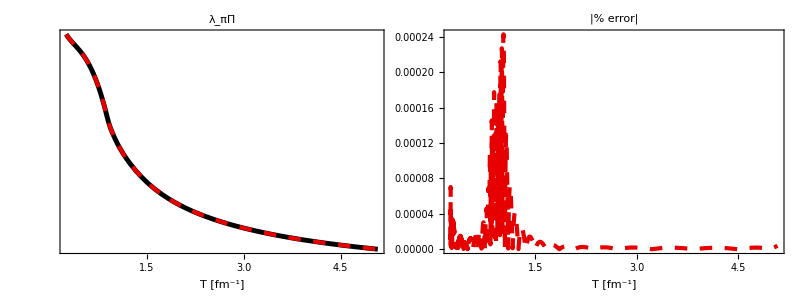

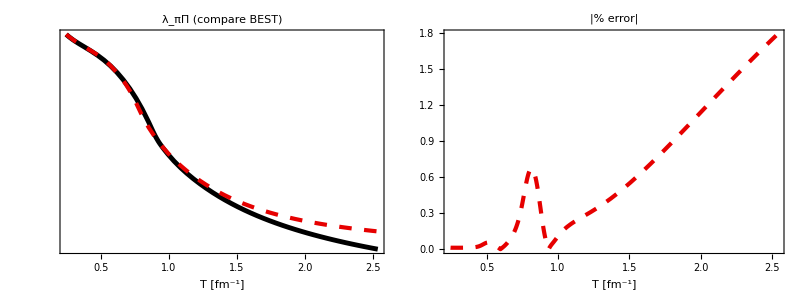

```mathematica
wd=SetDirectory@NotebookDirectory[];
cEbar= Interpolation[Import[wd<>"/beta_coefficients/results/cE_bar.dat"]];
cPbar= Interpolation[Import[wd<>"/beta_coefficients/results/cP_bar.dat"]];
I00= Interpolation[Import[wd<>"/beta_coefficients/results/I00.dat"]];
I01= Interpolation[Import[wd<>"/beta_coefficients/results/I01.dat"]];

lambdapibulk[T_]=6./5.  -  (2. mQuasifunc[T]^4)/15.(cEbar[T]*I00[T] + cPbar[T]*I01[T]) ;

lambdapibulkData=Table[{temp[[i]],lambdapibulk[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
lambdapibulkfit[T_]=rationalPolyFit[lambdapibulkData,n,n]/.{x->T};

lambdapibulkBEST[T_]:=(12.99206454463569-169.54052200735396*T+926.7433627872834*T^2-2737.729005326291*T^3+4894.186943117873*T^4-6808.352385039898*T^5+11455.103577067215*T^6-16223.412682922612*T^7-1726.4466539808268*T^8+51533.66615818827*T^9-71405.25614289886*T^10-11473.045592331333*T^11+150133.97086759048*T^12-225050.65838211164*T^13+216005.29370917648*T^14-195103.38216242057*T^15+185654.15734013912*T^16-151139.0928987391*T^17+86270.04307986688*T^18-29641.407324317806*T^19+4592.175198159571*T^20)/(6.942431024560642-83.25934313181178*T+372.4163321557213*T^2-540.4041791636039*T^3-1451.0176972731367*T^4+7760.53173158144*T^5-13745.493990457477*T^6+7380.613987314975*T^7+13872.501591214515*T^8-32252.74398590952*T^9+26461.959898609737*T^10+12906.06555162381*T^11-78629.42916778443*T^12+129713.94962826988*T^13-108503.32052649333*T^14+15229.21907703306*T^15+74506.79069856368*T^16-96441.18087908327*T^17+61933.9361101176*T^18-21899.948857152383*T^19+3401.8773149926765*T^20);

Grid[{{
LogPlot[{lambdapibulk[T],lambdapibulkfit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["λ_πΠ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(lambdapibulk[T]-lambdapibulkfit[T])/lambdapibulk[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Grid[{{
LogPlot[{lambdapibulk[T],lambdapibulkBEST[T]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["λ_πΠ (compare BEST)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(lambdapibulk[T]-lambdapibulkBEST[T])/lambdapibulk[T]]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["lambdapibulk.txt",CForm[lambdapibulkfit[T]]];
```

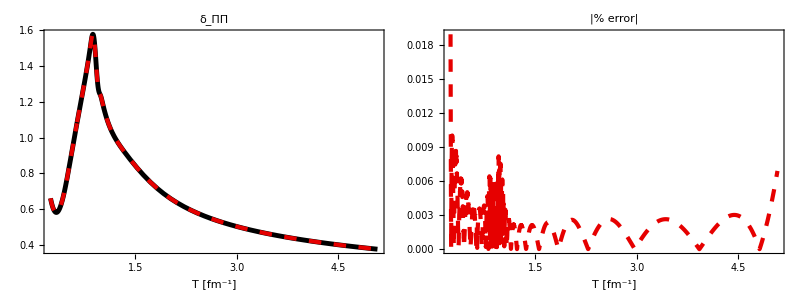

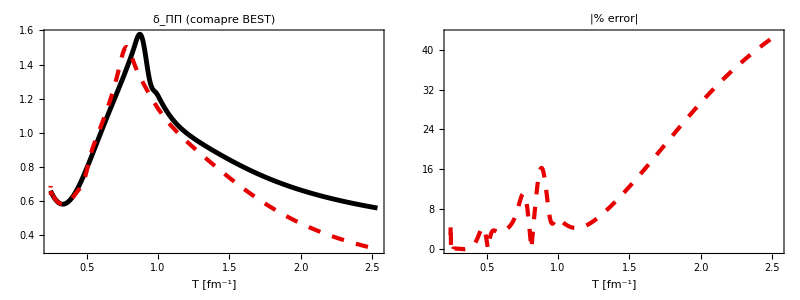

```mathematica
wd=SetDirectory@NotebookDirectory[];
cEbar= Interpolation[Import[wd<>"/beta_coefficients/results/cE_bar.dat"]];
cPbar= Interpolation[Import[wd<>"/beta_coefficients/results/cP_bar.dat"]];
I00= Interpolation[Import[wd<>"/beta_coefficients/results/I00.dat"]];
I01= Interpolation[Import[wd<>"/beta_coefficients/results/I01.dat"]];
I21= Interpolation[Import[wd<>"/beta_coefficients/results/I21.dat"]];
I22= Interpolation[Import[wd<>"/beta_coefficients/results/I22.dat"]];

deltabulkbulk[T_]=1.-cs2temp[T]  -  mQuasifunc[T]^4/9.(cEbar[T]*I00[T] + cPbar[T]*I01[T]) - mdmde[T](etemp[T]+Ptemp[T])(cEbar[T]*I21[T]+(5.*cPbar[T]*I22[T])/3. +3./mQuasifunc[T]^2);

deltabulkbulkData=Table[{temp[[i]],deltabulkbulk[temp[[i]]]},{i,1,Length[temp]}];

n = 22;
deltabulkbulkfit[T_]=rationalPolyFit[deltabulkbulkData,n,n]/.{x->T};


deltabulkbulkBEST[T_]:=(1.112464830627627-30.89549922917583*T+396.870006274666*T^2-3129.9976866790344*T^3+16932.514545225313*T^4-66299.23075219386*T^5+192274.86803468294*T^6-411200.446249874*T^7+614971.2968848197*T^8-502023.1644284749*T^9-273587.7966665477*T^10+1.7086212823445613*10^6*T^11-3.196746306338305*10^6*T^12+3.877749066174241*10^6*T^13-3.3898453966839234*10^6*T^14+2.185472078781732*10^6*T^15-1.032817317133193*10^6*T^16+348935.5353149965*T^17-80347.96558106475*T^18+11439.311285149332*T^19-765.3576755409805*T^20)/(0.37126794205159463-6.85080512583097*T+44.95316470829425*T^2-40.74867031423679*T^3-1259.8476683470476*T^4+9594.305515372564*T^5-37292.87815999376*T^6+89724.25271332267*T^7-130225.71895100547*T^8+75583.94325665919*T^9+99151.85661485561*T^10-222883.41719277928*T^11+19292.22932716292*T^12+541325.663364556*T^13-1.0859744865862972*10^6*T^14+1.2010209335366846*10^6*T^15-873622.406544788*T^16+430094.25540051*T^17-138701.1117796839*T^18+26384.77537231692*T^19-2210.019669868818*T^20);


Grid[{{
Plot[{deltabulkbulk[T],deltabulkbulkfit[T]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["δ_ΠΠ",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(deltabulkbulk[T]-deltabulkbulkfit[T])/deltabulkbulk[T]]},{T,Tmin,Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Grid[{{
Plot[{deltabulkbulk[T],deltabulkbulkBEST[T]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["δ_ΠΠ (comapre BEST)",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{100*Abs[(deltabulkbulk[T]-deltabulkbulkBEST[T])/deltabulkbulk[T]]},{T,Tmin,0.5Tmax},PlotRange->All,PlotStyle->styles,ImageSize->350,Frame->True,PlotLabel->Style["|% error|",FontSize->24],Axes->False,FrameLabel->{"T [fm^-1]",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["deltabulkbulk.txt",CForm[deltabulkbulkfit[T]]];
```

```mathematica
T0=0.5*GeVtoInversefm;
etemp[T0]
PL[T0]
Beqfunc[T0]
dBasy[0.5*GeVtoInversefm]
zQuasifunc[T0]
mQuasifunc[T0]
mdmde[T0]
zetas[T0/Tp]
betabulk[T0]
taubulk[T0]
```

563.822

PL[2.53387]

-4.79403

dBasy[2.53387]

1.16547

2.95314

0.00128613

zetas[2.53387/Tp]

1.81005

taubulk[2.53387]

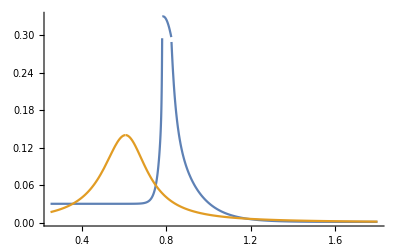

```mathematica
(* x = T / Tp *)
Tp = 0.155*GeVtoInversefm;
zetas[x_]:=Piecewise[{{0.9*Exp[-(x-1.)/0.025]+0.25*Exp[-(x-1.)/0.13]+0.001, x>1.05},{-13.77*x*x+27.55*x-13.45, 0.995≤ x≤ 1.05},{0.9*Exp[(x-1.)/0.0025]+0.22*Exp[(x-1.)/0.022]+0.03, x<0.995}}]

Tzeta=0.12*GeVtoInversefm;
w0=0.025*GeVtoInversefm;
l0=-0.03;
max0=0.14;

Lambda[T_]:=w0*(1.+l0*Sign[T-Tzeta]);
zetasNew[T_]:=(max0*Lambda[T]^2)/(Lambda[T]^2+(T-Tzeta)^2);

Plot[{zetas[T/Tp],zetasNew[T]},{T,0.05*GeVtoInversefm,0.355*GeVtoInversefm},PlotRange->All]

Clear[PL,bulk,taubulk,dBasy,dB2,t0]

PL[T_,ratio_]:=(3.*Ptemp[T]*ratio)/(2.+ratio);
PT[T_,ratio_]:=(3.*Ptemp[T])/(2.+ratio);
mdot[T_,ratio_,t0_]:=(-mdmde[T]*(etemp[T]+PL[T,ratio]))/(mQuasifunc[T]*t0);
bulk[T_]:=etemp[T]/3.-Ptemp[T];
(*taubulk[T_]:=(zetas[T/Tp]*Sfit1[T])/betabulk[T];*)
taubulk[T_]:=(zetasNew[T]*Sfit1[T])/betabulk[T];

dBasy[T_,ratio_,t0_]:=(3.*taubulk[T]*mdot[T,ratio,t0]*bulk[T])/(mQuasifunc[T]-4.*taubulk[T]*mdot[T,ratio,t0]);

dB2[T_,t0_]:=(-3.*taubulk[T]*mdmde[T]*bulk[T])/mQuasifunc[T]^2*(etemp[T]+Ptemp[T])/t0;

Manipulate[LogLinearPlot[{Beqfunc[T]+dBasy[T,ratio,t0],Beqfunc[T]+dB2[T,t0],Beqfunc[T]},{T,Tmin,Tmax},PlotStyle->{Red,Black,Blue},Frame->True,PlotRange->{-2,6},ImageSize->600],{{t0,0.25},0.25,5.25,0.05},{{ratio,1},0,1,0.05}]
```

```mathematica
Manipulate[LogLinearPlot[{PL[T,ratio]+Beqfunc[T]+dBasy[T,ratio,t0],PL[T,ratio]+Beqfunc[T]+dB2[T,t0],PL[T,ratio]+Beqfunc[T],PL[T,ratio]},{T,Tmin,Tmax},Frame->True,Axes->{True,False},PlotStyle->{Red,Black,Blue,Green},PlotRange->{-0.01,0.01},ImageSize->600],{{t0,0.5},0.25,5.25,0.05},{{ratio,0.2},0,1,0.05}]
```

```mathematica
Manipulate[LogLinearPlot[{etemp[T],etemp[T]-Beqfunc[T]-dBasy[T,ratio,t0],etemp[T]-Beqfunc[T]-dB2[T,t0]},{T,Tmin,Tmax},Frame->True,PlotStyle->{Blue,Red,Black},PlotRange->{-10,40},ImageSize->800],{{t0,0.5},0.25,5.25,0.05},{{ratio,1},0,1,0.01}]
```

```mathematica
Manipulate[LogLinearPlot[{Beqfunc[T],Beqfit[T]},{T,Tmin,Tmax},PlotStyle->{Red,Black},Frame->True,PlotRange->{-0.1,0.42},ImageSize->600],{{t0,0.25},0.25,5.25,0.05},{{ratio,1},0,1,0.05}]
```

```mathematica
Manipulate[LogLinearPlot[{PL[T,ratio]+Beqfunc[T],PT[T,ratio]+Beqfunc[T],etemp[T]-Beqfunc[T]},{T,Tmin,Tmax},PlotStyle->{Red,Black,Blue},Frame->True,PlotRange->{-0.1,10},ImageSize->600],{{ratio,0.1},0,1,0.05}]
```

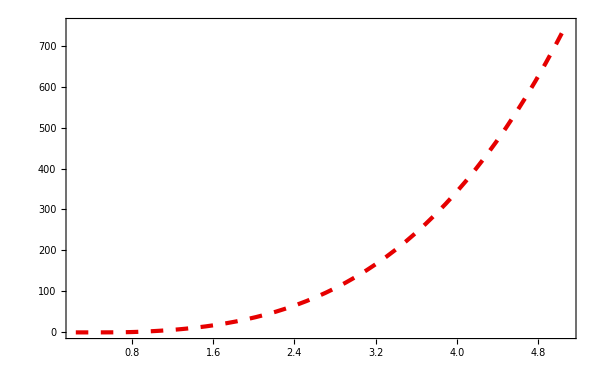

```mathematica
Plot[{etemp[T]-3.*Ptemp[T]-4.*Beqfunc[T]},{T,Tmin,Tmax},PlotStyle->styles,Frame->True,ImageSize->600]
```

```mathematica
Manipulate[LogLinearPlot[{0,PL[T,ratio]+Beqfunc[T]},{T,Tmin,Tmax},PlotStyle->{Black,Red},Frame->True,PlotRange->{-0.001,0.001},ImageSize->600],{{ratio,0.35},0,1,0.05}]
```